# Simple Example

## n to n transition

Exact Result

```mathematica
Clear[θ]
4/(2π Sin[2θ])
```

(2 Csc[2 θ])/π

Bare Parameters

```mathematica
Clear[δ,θ]
a=1/4;
b=(1/2-Sin[θ]^2+ⅈ δ);
```

```mathematica
Clear[θ,δ];
Exact=ⅈ/(2π)Sum[Binomial[2M,M] a^(2M)/b^(2 M+1),{M,0,∞}];
FullSimplify[Limit[Exact,δ->0]]
```

```mathematica
(ⅈ Sec[2 θ])/(π √(-Tan[2 θ]^2))
```

Renormalization Flow of y = 1/b and x = b/a

```mathematica
y[0]=1/b;
x[0]=b/a;
x[1]=x[0]^2-2;
y[1]=y[0]*1/(1-2/x[0]^2);
```

Renormalized Sum converges to the same exact expression

```mathematica
Exact1=ⅈ/(2π) y[1]Sum[Binomial[2M,M] 1/x[1]^(2M),{M,0,∞}];
```

```mathematica
Limit[Exact1,δ->0]
```

(2 ⅈ Cos[2 θ] Sec[4 θ])/(π √(-Tan[4 θ]^2))

Now we see how well the first term approximates the exact answer under renorm group.

```mathematica
Clear[θ,δ]
y[0]=1/b;
x[0]=b/a;
For[n=0,n≤50,n++, x[n+1]=x[n]^2-2];
For[n=0,n≤50,n++, y[n+1] =y[n] 1/(1-2/x[n]^2)];
```

We see that if keep turning the crank the first term approaches the exact answer!

```mathematica
θ=π/4;
δ=0.0001;
4./(2π Sin[2θ])
```

0.63662

```mathematica
Renorm=Table[2Re[ⅈ/(2π)y[n]],{n,1,30}];
```

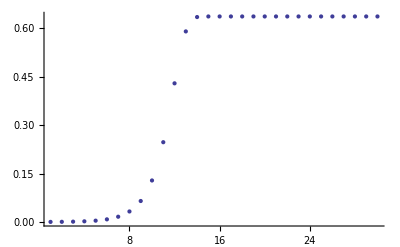

```mathematica
ListPlot[Renorm]
```